```mathematica
$Assumptions = {x ∈ Reals, y ∈ Reals, ϵ ∈ Reals, k ∈ Integers, ϕ ∈ Reals, a ∈ Reals, d ∈ Reals, v ∈ Reals}
```

{x∈ℝ,y∈ℝ,ϵ∈ℝ,k∈ℤ,ϕ∈ℝ,a∈ℝ,d∈ℝ,v∈ℝ}

## Preliminaries

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
q = x + I y
```

x+ⅈ y

```mathematica
f1 =FullSimplify[Δ + α (q + Conjugate[q])]
f3 = FullSimplify[Δ + α (ω q + Conjugate[ω q])]
f5 = FullSimplify[Δ + α (Conjugate[ω] q + ω Conjugate[q])]
```

2 x α+Δ

-((x+√3 y) α)+Δ

-x α+√3 y α+Δ

## Char Poly

```mathematica
H = FullSimplify[{{v * (q + Conjugate[q]), f3, Conjugate[f5]}, {Conjugate[f3], v * (ω q + Conjugate[ω q]), f1}, {f5, Conjugate[f1], v*(Conjugate[ω] q + ω Conjugate[q]) }}]
```

{{2 v x,-((x+√3 y) α)+Δ,Conjugate[-x α+√3 y α+Δ]},{Conjugate[-((x+√3 y) α)+Δ],-v (x+√3 y),2 x α+Δ},{-x α+√3 y α+Δ,Conjugate[2 x α+Δ],v (-x+√3 y)}}

```mathematica
poly = FullSimplify[ComplexExpand[CharacteristicPolynomial[H, ϵ], {α, Δ}]]
```

2 v^3 (x^3-3 x y^2)+(2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+3 v^2 (x^2+y^2) ϵ-ϵ^3+6 (-v (x (x^2+y^2) α+(x-y) (x+y) Δ)+(x^2+y^2) α ϵ) Conjugate[α]+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ] (6 v (-x^2+y^2) α+3 Δ ϵ+Conjugate[Δ]^2)

```mathematica
polyex = Collect[Expand[poly], {ϵ}, FullSimplify]
```

2 x (x^2-3 y^2) (v^3+α^3)-3 (x^2+y^2) α^2 Δ+Δ^3-ϵ^3-6 v (x (x^2+y^2) α+(x-y) (x+y) Δ) Conjugate[α]+2 x (x^2-3 y^2) Conjugate[α]^3+6 v (-x^2+y^2) α Conjugate[Δ]-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3+ϵ (3 (x^2+y^2) (v^2+2 α Conjugate[α])+3 Δ Conjugate[Δ])

```mathematica
FullSimplify[ComplexExpand[Coefficient[polyex, ϵ, 0], {α, Δ}]]
```

2 x (x^2-3 y^2) (v^3+α^3)-3 (x^2+y^2) α^2 Δ+Δ^3-6 v (x (x^2+y^2) α+(x-y) (x+y) Δ) Conjugate[α]+2 x (x^2-3 y^2) Conjugate[α]^3+6 v (-x^2+y^2) α Conjugate[Δ]-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3

## Eigenvalues

```mathematica
b = FullSimplify[6 α Conjugate[α] (x^2 + y^2) + 3 Δ Conjugate[Δ]]
c = FullSimplify[4 Re[α^3] x^3 - 6 Re[α^2 Δ] x^2 - 6 Re[α^2 Δ] y^2 - 12 Re[α^3] x y^2 + 2 Re[Δ^3]]
ϵ = FullSimplify[2 Sqrt[b/3] Cos[1/3 ArcCos[(3 c)/(2 b) Sqrt[3/b] - 0* 2 π/3]]]
```

6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]

2 (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])

2 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]

## Eigenvectors

```mathematica
nmz = ϵ^6 + ϵ^4 (f3 Conjugate[f3] - 2 f1 Conjugate[f1] - 2 f5 Conjugate[f5]) - 2 ϵ^3 Re[f1 f3 f5] + ϵ^2 ((f1 Conjugate[f1])^2 + (f5 Conjugate[f5])^2+ 2 f1 Conjugate[f1] f5 Conjugate[f5] - 2 f1 Conjugate[f1] f3 Conjugate[f3] + f3 Conjugate[f3] f5 Conjugate[f5]) + 2 ϵ Re[f1 f3 f5] (f1 Conjugate[f1] + f3 Conjugate[f3] + f5 Conjugate[f5])+ f1 Conjugate[f1] f3 Conjugate[f3] (f1 Conjugate[f1] + f3 Conjugate[f3] + f5 Conjugate[f5])
```

(2 x α+Δ) (-((x+√3 y) α)+Δ) Conjugate[2 x α+Δ] Conjugate[-((x+√3 y) α)+Δ] ((2 x α+Δ) Conjugate[2 x α+Δ]+(-x α+√3 y α+Δ) Conjugate[-x α+√3 y α+Δ]+(-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ])+4 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) ((2 x α+Δ)^2 Conjugate[2 x α+Δ]^2+2 (2 x α+Δ) (-x α+√3 y α+Δ) Conjugate[2 x α+Δ] Conjugate[-x α+√3 y α+Δ]+(-x α+√3 y α+Δ)^2 Conjugate[-x α+√3 y α+Δ]^2-2 (2 x α+Δ) (-((x+√3 y) α)+Δ) Conjugate[2 x α+Δ] Conjugate[-((x+√3 y) α)+Δ]+(-x α+√3 y α+Δ) (-((x+√3 y) α)+Δ) Conjugate[-x α+√3 y α+Δ] Conjugate[-((x+√3 y) α)+Δ]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^2+16 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α])^2 (-2 (2 x α+Δ) Conjugate[2 x α+Δ]-2 (-x α+√3 y α+Δ) Conjugate[-x α+√3 y α+Δ]+(-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^4+64 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α])^3 Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^6+4 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) ((2 x α+Δ) Conjugate[2 x α+Δ]+(-x α+√3 y α+Δ) Conjugate[-x α+√3 y α+Δ]+(-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]] Re[(2 x α+Δ) (-x α+√3 y α+Δ) (-((x+√3 y) α)+Δ)]-16 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α])^(3/2) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^3 Re[(2 x α+Δ) (-x α+√3 y α+Δ) (-((x+√3 y) α)+Δ)]

```mathematica
A1 = Sqrt[f3 Conjugate[f3]] * (ϵ^2 - f1 Conjugate[f1])
A3 = Conjugate[f3]/Sqrt[f3 Conjugate[f3]] (ϵ (ϵ^2 - f1 Conjugate[f1]) - Conjugate[f5] (ϵ f5 + Conjugate[f1] Conjugate[f3]))
A5 = Sqrt[f3 Conjugate[f3]] (ϵ f5 + Conjugate[f1] Conjugate[f3])
```

√((-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ]) (-((2 x α+Δ) Conjugate[2 x α+Δ])+4 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^2)

(Conjugate[-((x+√3 y) α)+Δ] (-Conjugate[-x α+√3 y α+Δ] (Conjugate[2 x α+Δ] Conjugate[-((x+√3 y) α)+Δ]+2 (-x α+√3 y α+Δ) √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]])+2 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]] (-((2 x α+Δ) Conjugate[2 x α+Δ])+4 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]]^2)))/(√((-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ]))

√((-((x+√3 y) α)+Δ) Conjugate[-((x+√3 y) α)+Δ]) (Conjugate[2 x α+Δ] Conjugate[-((x+√3 y) α)+Δ]+2 (-x α+√3 y α+Δ) √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3 √3 (1/(6 (x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) (2 (x^3-3 x y^2) Re[α^3]-3 (x^2+y^2) Re[α^2 Δ]+Re[Δ^3])]])

## Useful Computations

```mathematica
Clear[Δ, α, k]
```

```mathematica
nmz0 = FullSimplify[ComplexExpand[64 Re[ω^k Δ]^6 - 48 Abs[Δ]^2 Re[ω^k Δ]^4 - 16 Re[Δ^3] Re[ω^k Δ]^3 + 12 Abs[Δ]^4 Re[ω^k Δ]^2 + 12 Abs[Δ]^2 Re[Δ^3] Re[ω^k Δ] + 3 Abs[Δ]^6, {α, Δ}]]
```

3 Abs[Δ]^2 ((Δ^2+Conjugate[Δ]^2) Cos[(4 k π)/3]+Im[Δ]^2+Re[Δ]^2-4 Im[Δ] Re[Δ] Sin[(4 k π)/3])^2

```mathematica
term3 = FullSimplify[ComplexExpand[(-2 Sqrt[3])/nmz0^2 Re[α Conjugate[Δ]] (48 Abs[Δ]^2 Re[ω^k Δ]^2 - 12 Abs[Δ]^4) (Im[α Conjugate[Δ]]/(2 Abs[Δ]^2) Abs[8 Re[ω^k Δ]^3 - 4 Abs[Δ]^2 Re[ω^k Δ] - Δ^3]^2 + 2 Re[α Conjugate[Δ]] Re[ω^k Δ] Im[Δ^3]), {α, Δ}]]
```

-((4 (Im[α] Im[Δ]+Re[α] Re[Δ]) (ⅇ^(-8/3 ⅈ k π) (2 ⅇ^((16 ⅈ k π)/3) Δ^4+3 ⅇ^((8 ⅈ k π)/3) Abs[Δ]^4+3 Δ^3 Conjugate[Δ]+3 ⅇ^((4 ⅈ k π)/3) Δ Conjugate[Δ]^3+2 Conjugate[Δ]^4) Re[Δ Im[α]-α Im[Δ]]+Im[α Im[Δ]^4+2 Im[Δ]^2 Re[Δ] (2 Δ Re[α]-3 α Re[Δ])+Re[Δ]^3 (-4 Δ Re[α]+α Re[Δ])] (-4 Cos[(2 k π)/3] Re[Δ]+4 Im[Δ] Sin[(2 k π)/3])))/(√3 Abs[Δ]^2 ((Δ^2+Conjugate[Δ]^2) Cos[(4 k π)/3]+Im[Δ]^2+Re[Δ]^2-4 Im[Δ] Re[Δ] Sin[(4 k π)/3])^3))

```mathematica
term5 = FullSimplify[ComplexExpand[(4 Sqrt[3])/nmz0 Re[α Conjugate[Δ]] (4 Re[ω^k Δ]^2 Im[α Conjugate[Δ]] + 4 Re[ω^k Δ] Im[α Δ^2] + Abs[Δ]^2 Im[α Conjugate[Δ]]) ((12 Abs[Δ]^2)/nmz0 Re[ω^k Δ]^2 (Abs[Δ]^2 - 4 Re[ω^k Δ]^2) + 1), {α, Δ}]]
```

-((4 (Im[α] Im[Δ]+Re[α] Re[Δ]) (4 Cos[(2 k π)/3] Im[1/2 α (Δ^2+Conjugate[Δ]^2)+2 Δ Re[α] Re[Δ]] Re[Δ]+3 Abs[Δ]^2 Re[Δ Im[α]-α Im[Δ]]+2 Cos[(4 k π)/3] (Im[Δ]^2-Re[Δ]^2) Re[-Δ Im[α]+α Im[Δ]]+4 Im[Δ] Im[α Im[Δ]^2-Re[Δ] (2 Δ Re[α]+α Re[Δ])] Sin[(2 k π)/3]+4 Im[Δ] Re[Δ] Re[-Δ Im[α]+α Im[Δ]] Sin[(4 k π)/3]))/(√3 ((Δ^2+Conjugate[Δ]^2) Cos[(4 k π)/3]+Im[Δ]^2+Re[Δ]^2-4 Im[Δ] Re[Δ] Sin[(4 k π)/3])^3))

```mathematica
k = 2
```

2

```mathematica
Δ = d Exp[I ϕ]
α = a Exp[I θ]
```

d ⅇ^(ⅈ ϕ)

a ⅇ^(ⅈ θ)

```mathematica
Ω = FullSimplify[ComplexExpand[(term3 + term5), {α, Δ}]]
```

1/(3 d^2 (-1+√3 Cot[ϕ])^3)a^2 Cos[θ-ϕ] Csc[ϕ]^3 (6 (-1+√3 Cot[ϕ]) Sin[θ]-Cos[θ] Csc[ϕ]^2 (5 √3+√3 Cos[2 ϕ]-9 Sin[2 ϕ]))

```mathematica
temp = FullSimplify[Sin[ϕ]^2*(6 (-1+√3 Cot[ϕ]) Sin[θ]-Cos[θ] Csc[ϕ]^2 (5 √3+√3 Cos[2 ϕ]-9 Sin[2 ϕ]))]
```

6 (-1+√3 Cot[ϕ]) Sin[θ] Sin[ϕ]^2-Cos[θ] (5 √3+√3 Cos[2 ϕ]-9 Sin[2 ϕ])

```mathematica
temp2 = FullSimplify[Sin[ϕ] (-2 * Cos[θ + ϕ + π/6] + Cos[θ - ϕ + π/2])]
```

-((2 Cos[π/6+θ+ϕ]+Sin[θ-ϕ]) Sin[ϕ])

```mathematica
FullSimplify[4 π/3+π/6]
```

(3 π)/2

```mathematica
FullSimplify[Sin[ϕ]^2*temp - temp2]
```

Sin[ϕ] (2 Cos[π/6+θ+ϕ]+Sin[θ-ϕ]+6 (-1+√3 Cot[ϕ]) Sin[θ] Sin[ϕ]^3-Cos[θ] Sin[ϕ] (5 √3+√3 Cos[2 ϕ]-9 Sin[2 ϕ]))

```mathematica
FullSimplify[emp]
```

Sin[ϕ]^2 (-6 Sin[θ] Sin[ϕ] (√3 Cos[ϕ]+Sin[ϕ])+Cos[θ] (5 √3+√3 Cos[2 ϕ]+9 Sin[2 ϕ]))

```mathematica
TrigReduce[-6 Sin[θ] Sin[ϕ] (√3 Cos[ϕ]+Sin[ϕ])+Cos[θ] (5 √3+√3 Cos[2 ϕ]+9 Sin[2 ϕ])]
```

5 √3 Cos[θ]-√3 Cos[θ-2 ϕ]+2 √3 Cos[θ+2 ϕ]-3 Sin[θ]-3 Sin[θ-2 ϕ]+6 Sin[θ+2 ϕ]

```mathematica
Clear[ϕ, θ, a, d]
```

```mathematica
ϕ =FullSimplify[ 1/2 (2*2 π/3 + ArcSin[x] + ArcSin[2 x])]
θ =FullSimplify[ 1/2 (2*2 π/3 + ArcSin[x] - ArcSin[2 x])]
```

1/2 ((4 π)/3+ArcSin[x]+ArcSin[2 x])

1/6 (4 π+3 ArcSin[x]-3 ArcSin[2 x])

```mathematica
Clear[θ, ϕ]
```

```mathematica
ϕ0 =FullSimplify[ 1/2 (0*2 π/3 + ArcSin[x] + ArcSin[2 x])]
θ0 =FullSimplify[ 1/2 (0*2 π/3 + ArcSin[x] - ArcSin[2 x])]
ϕ1 =FullSimplify[ 1/2 (1*2 π/3 + ArcSin[x] + ArcSin[2 x])]
θ1 =FullSimplify[ 1/2 (1*2 π/3 + ArcSin[x] - ArcSin[2 x])]
ϕ2 =FullSimplify[ 1/2 (2*2 π/3 + ArcSin[x] + ArcSin[2 x])]
θ2 =FullSimplify[ 1/2 (2*2 π/3 + ArcSin[x] - ArcSin[2 x])]
```

1/2 (ArcSin[x]+ArcSin[2 x])

1/2 (ArcSin[x]-ArcSin[2 x])

1/2 ((2 π)/3+ArcSin[x]+ArcSin[2 x])

1/6 (2 π+3 ArcSin[x]-3 ArcSin[2 x])

1/2 ((4 π)/3+ArcSin[x]+ArcSin[2 x])

1/6 (4 π+3 ArcSin[x]-3 ArcSin[2 x])

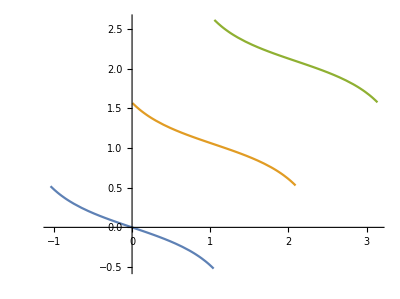

```mathematica
ParametricPlot[{{ϕ0, θ0}, {ϕ1, θ1}, {ϕ2, θ2}}, {x, -1, 1}]
```